```mathematica
(* Сковлюк Г.Р. 221701 Вариант 4* )
```

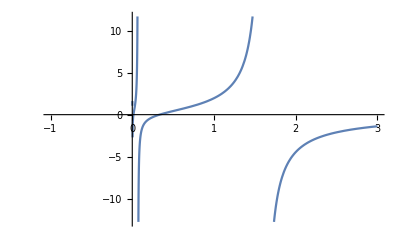

```mathematica
f[x_]:=Tan[Log[3x]];
Subscript[x, 0]=2.13;
graph=Plot[f[x],{x,-1,3}];
Show[graph]
```

```mathematica
d11=D[f[x],x]/.x->Subscript[x, 0]
d21=D[f[x],{x,2}]/.x->Subscript[x, 0]
```

5.98241

-22.0576

```mathematica
FiniteDiff1[y_,y1_]:=y1-y;
FiniteDiff2[y_,y1_,y2_]:=y2-2y1+y;
FiniteDiff3[y_,y1_,y2_,y3_]:=y3-3y2+3y1-y;
```

```mathematica
h=0.1
```

0.1

```mathematica
y1=1/h(FiniteDiff1[f[Subscript[x, 0]],f[Subscript[x, 0]+h]]-1/2*FiniteDiff2[f[Subscript[x, 0]],f[Subscript[x, 0]+h],f[Subscript[x, 0]+2h]]+1/3*FiniteDiff3[f[Subscript[x, 0]],f[Subscript[x, 0]+h],f[Subscript[x, 0]+2h], f[Subscript[x, 0]+3h]])
```

5.89013

```mathematica
y2=1/h^2(FiniteDiff2[f[Subscript[x, 0]],f[Subscript[x, 0]+h],f[Subscript[x, 0]+2h]]-FiniteDiff3[f[Subscript[x, 0]],f[Subscript[x, 0]+h],f[Subscript[x, 0]+2h], f[Subscript[x, 0]+3h]])
```

-18.3234

```mathematica
{Abs[d11-y1],Abs[d21-y2]}
```

{0.0922838,3.73421}

```mathematica
h=0.01
```

0.01

```mathematica
y1=1/h(FiniteDiff1[f[Subscript[x, 0]],f[Subscript[x, 0]+h]]-1/2*FiniteDiff2[f[Subscript[x, 0]],f[Subscript[x, 0]+h],f[Subscript[x, 0]+2h]]+1/3*FiniteDiff3[f[Subscript[x, 0]],f[Subscript[x, 0]+h],f[Subscript[x, 0]+2h], f[Subscript[x, 0]+3h]])
y2=1/h^2(FiniteDiff2[f[Subscript[x, 0]],f[Subscript[x, 0]+h],f[Subscript[x, 0]+2h]]-FiniteDiff3[f[Subscript[x, 0]],f[Subscript[x, 0]+h],f[Subscript[x, 0]+2h], f[Subscript[x, 0]+3h]])
```

5.9822

-21.9788

```mathematica
{Abs[d11-y1],Abs[d21-y2]}
```

{0.000212733,0.0788102}

```mathematica
(*Вывод:Исходя из вышеприведенных вычислений очевидно, что уменьшение шага при вычеслении дифференциала приводит к более точным результатам.*)
```

```mathematica
(* 2 а) *)
```

```mathematica
f[x_]:=Sinh[Log[Cosh[x]]]
```

```mathematica
h=0.2;
a=-1;
b=3;
data=Table[{x,(f[x+h]-f[x-h])/(2h)},{x,a,b,h}];
TableForm[data,TableHeadings->{Table[i,{i,(b-a)/h+1}],{"x_i","y'_i"}}]
```

| x_i | y'_i
1 | -1. | -0.835793
2 | -0.8 | -0.69139
3 | -0.6 | -0.542088
4 | -0.4 | -0.37772
5 | -0.2 | -0.195081
6 | 0. | 0.
7 | 0.2 | 0.195081
8 | 0.4 | 0.37772
9 | 0.6 | 0.542088
10 | 0.8 | 0.69139
11 | 1. | 0.835793
12 | 1.2 | 0.988688
13 | 1.4 | 1.1639
14 | 1.6 | 1.37461
15 | 1.8 | 1.63363
16 | 2. | 1.95415
17 | 2.2 | 2.35075
18 | 2.4 | 2.84035
19 | 2.6 | 3.44321
20 | 2.8 | 4.18383
21 | 3. | 5.09213

```mathematica
(* б) *)
```

```mathematica
derivateOfFunc=D[f[x],x]
```

Sinh[x]-1/2 (-1+Cosh[x]^2) Sech[x] Tanh[x]

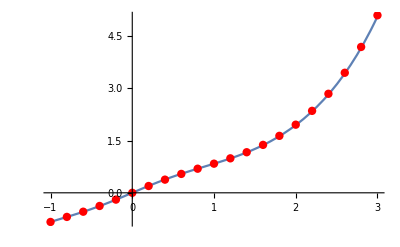

```mathematica
graph=Plot[derivateOfFunc,{x,-1,3}];
dots=ListPlot[data,PlotStyle->{PointSize[0.015],Red}];
Show[graph,dots]
```

```mathematica
(* 3 а) *)
```

```mathematica
f[x_]:=((x^2+6)^(1/2))/(3*x+(x^2+0.6)^(1/2))
a=0.7;
b=1.5;
n1=8;
Subscript[x, 0]=a;
step=(b-a)/n1;
```

```mathematica
For[i=1,i<=n1,i++,
Subscript[x, i]=step+Subscript[x, i-1];]
```

```mathematica
averageRectangle1=(b-a)/n1*∑_(i=1)^n1 f[Subscript[x, i-1]+(b-a)/(2*n1)]
```

4.265

```mathematica
n2=10;
step=(b-a)/n2;
For[i=1,i<=n2,i++,
Subscript[x, i]=step+Subscript[x, i-1];]
```

```mathematica
averageRectangle2=(b-a)/n2*∑_(i=1)^n2 f[Subscript[x, i-1]+(b-a)/(2*n2)]
```

4.28847

```mathematica
k=2;
Richardson=averageRectangle2+n1^k/(n2^k-n1^k)(averageRectangle2-averageRectangle1)
```

4.33022

```mathematica
(* б) *)
```

```mathematica
n1=8;
Subscript[x, 0]=a;
step=(b-a)/n1;
For[i=1,i<=n1,i++,
Subscript[x, i]=step+Subscript[x, i-1];]
trapezoid1=(b-a)/n1*(∑_(i=1)^(n1-1) f[Subscript[x, i]]+f[Subscript[x, 0]]/2+f[Subscript[x, n1]]/2)
```

4.54122

```mathematica
n2=10;
Subscript[x, 0]=a;
step=(b-a)/n2;
For[i=1,i<=n2,i++,
Subscript[x, i]=step+Subscript[x, i-1];]
trapezoid2=(b-a)/n2*(∑_(i=1)^(n2-1) f[Subscript[x, i]]+f[Subscript[x, 0]]/2+f[Subscript[x, n2]]/2)
```

4.47902

```mathematica
Richardson=trapezoid2+n1^k/(n2^k-n1^k)(trapezoid2-trapezoid1)
```

4.36846

```mathematica
(* 4 *)
```

```mathematica
data=({{1.2, 0.1823}, {1.4, 0.3365}, {1.6, 0.4700}, {1.8, 0.5878}, {2., 0.6931}, {2.2, 0.7885}, {2.4, 0.8755}, {2.6, 0.9555}, {2.8, 1.0296}});
a=1.2;
b=2.8;
n=4;
h=(b-a)/(2n)
For[i=0,i<=2*n,i++,
Subscript[y, i]=data[[i+1,2]];
]
SimpsonFormula=∑_(i=0)^(n-1) h/3*(Subscript[y, 2i]+4 Subscript[y, 2i+1]+Subscript[y, 2i+2])
```

0.2

1.06415

```mathematica
data=({{1.2
1.3, 0.1823
0.2624}, {1.4
1.5, 0.3365
0.4055}, {1.6
1.7, 0.4700
0.5306}, {1.8
1.9, 0.5878
0.6419}, {2.
2.1, 0.6931
0.7419}, {2.2
2.3, 0.7885
0.8329}, {2.4
2.5, 0.8755
0.9163}, {2.6
2.7, 0.9555
0.9933}, {2.8, 1.0296}});
n=8;
h=(b-a)/(2n)
For[i=0,i<=2*n,i++,
Subscript[y, i]=data[[i+1,2]];
]
```

0.1

```mathematica
SimpsonFormula=∑_(i=0)^(n-1) h/3*(Subscript[y, 2i]+4 Subscript[y, 2i+1]+Subscript[y, 2i+2])
```

1.06837

```mathematica
(*5*)
f[x_]=Log[2x]/(4x+1);
a=1.1;
b=2;
n=4;
LegendreP[n,t]
```

1/8 (3-30 t^2+35 t^4)

```mathematica
sl=NSolve[LegendreP[n,t]==0,t]
```

{{t→-0.861136},{t→-0.339981},{t→0.339981},{t→0.861136}}

```mathematica
tt=t/.sl
```

{-0.861136,-0.339981,0.339981,0.861136}

```mathematica
T=Table[If[i==1,1,(tt[[j]])^(i-1)],{i,n},{j,n}];MatrixForm[T]
```

(1 | 1 | 1 | 1
-0.861136 | -0.339981 | 0.339981 | 0.861136
0.741556 | 0.115587 | 0.115587 | 0.741556
-0.638581 | -0.0392974 | 0.0392974 | 0.638581)

```mathematica
B=Table[If[EvenQ[i]==True,0,2/i],{i,n}]//N
```

{2.,0.,0.666667,0.}

```mathematica
A=LinearSolve[T,B]
```

{0.347855,0.652145,0.652145,0.347855}

```mathematica
int=(b-a)/2*∑_(i=1)^n A[[i]]*f[(b+a)/2+(b-a)/2*tt[[i]]]
```

0.139416

```mathematica
PaddedForm[int, {19,18}]
```

0.139415633641599600